## Misc

```mathematica
Πpar[θ_,v_,mD_]:=mD^2/2((2-2 v^2-v^4 Cos[θ]^2 Sin[θ]^2)/((1-v^2 Sin[θ]^2)^2)-((2+v^2 Sin[θ]^2)(1-v^2)v Cos[θ])/(2(1-v^2 Sin[θ]^2)^(5/2))Log[(v Cos[θ]+√(1-v^2 Sin[θ]^2))/(v Cos[θ]-√(1-v^2 Sin[θ]^2))]);
Πper[θ_,β_,v_,mD_]:=mD^2/2((2-2 v^2-v^4 Cos[β]^2 Sin[θ]^2(1-Cos[β]^2 Sin[θ]^2))/((1-v^2+v^2 Cos[β]^2 Sin[θ]^2)^2)-((2+v^2-v^2 Cos[β]^2 Sin[θ]^2)(1-v^2)v Cos[β]Sin[θ])/(2(1-v^2+v^2 Cos[β]^2 Sin[θ]^2)^2)Log[(v Cos[β]Sin[θ]+√(1-v^2+v^2 Cos[β]^2 Sin[θ]^2))/(v Cos[β]Sin[θ]-√(1-v^2+v^2 Cos[β]^2 Sin[θ]^2))]);
```

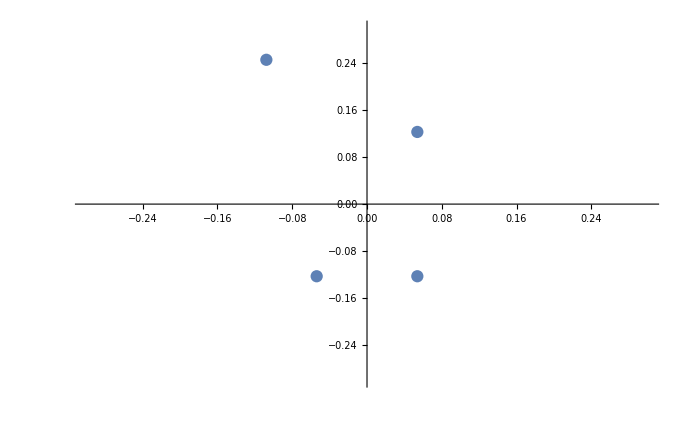

```mathematica
θ=0.;
ListPlot[{{Re[ⅈ √Πpar[θ,0.5,0.15]],Im[ⅈ √Πpar[θ,0.5,0.15]]},{Re[-ⅈ √Πpar[θ,0.5,0.15]],Im[-ⅈ √Πpar[θ,0.5,0.15]]},2{Re[ⅈ √Conjugate[Πpar[θ,0.5,0.15]]],Im[ⅈ √Conjugate[Πpar[θ,0.5,0.15]]]},{Re[-ⅈ √Conjugate[Πpar[θ,0.5,0.15]]],Im[-ⅈ √Conjugate[Πpar[θ,0.5,0.15]]]}},PlotRange->{{-0.3,0.3},{-0.3,0.3}}]
```

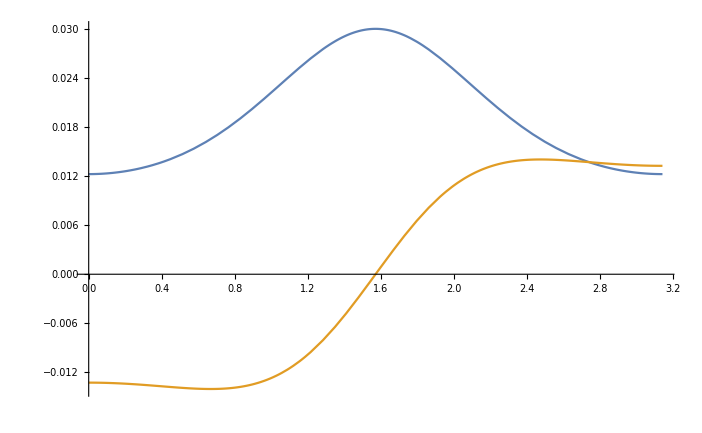

```mathematica
Plot[{Re[Πpar[θ,0.5,0.15]],Im[Πpar[θ,0.5,0.15]]},{θ,0,π}]
```

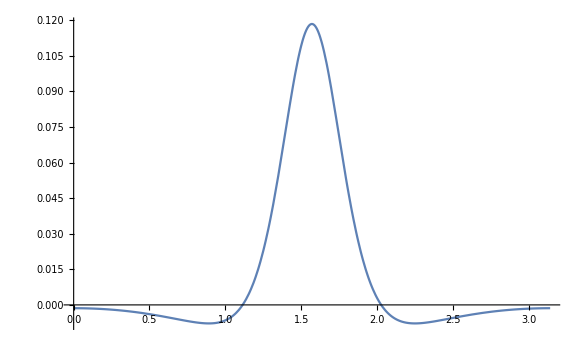

```mathematica
Plot[Re[Πpar[θ,0.9,0.15]],{θ,0,π}]
```

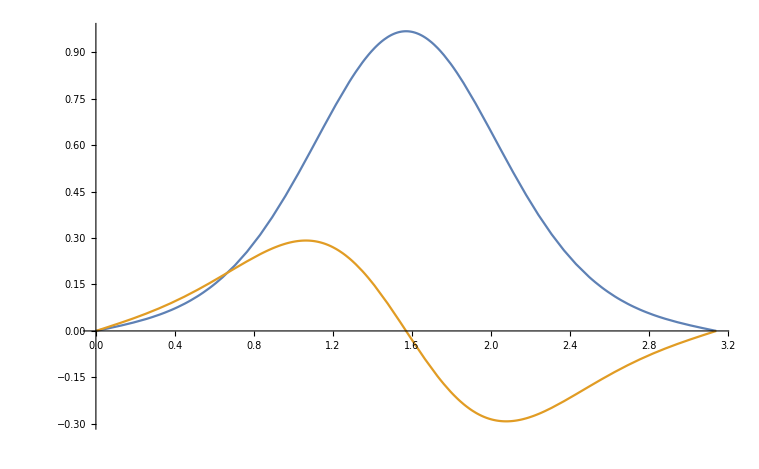

```mathematica
p=1;
mD=0.15;
r=1;
Plot[{Re[(Sin[x](v^2+v^2 Sin[x]^2))/((1-v^2 Sin[x]^2)^(5/2))Exp[ⅈ p r Cos[x]]/((p^2+Πpar[x,v,mD])(p^2+Conjugate[Πpar[x,v,mD]]))],Im[(Sin[x](v^2+v^2 Sin[x]^2))/((1-v^2 Sin[x]^2)^(5/2))Exp[ⅈ p r Cos[x]]/((p^2+Πpar[x,v,mD])(p^2+Conjugate[Πpar[x,v,mD]]))]},{x,0,π}]
```

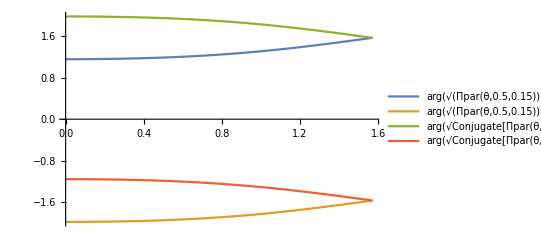

```mathematica
Plot[{Arg[√Πpar[θ,0.5,0.15]]+π/2,Arg[√Πpar[θ,0.5,0.15]]-π/2,Arg[√Conjugate[Πpar[θ,0.5,0.15]]]+π/2,Arg[√Conjugate[Πpar[θ,0.5,0.15]]]-π/2},{θ,0,π/2},PlotLegends->"Expressions"]
```

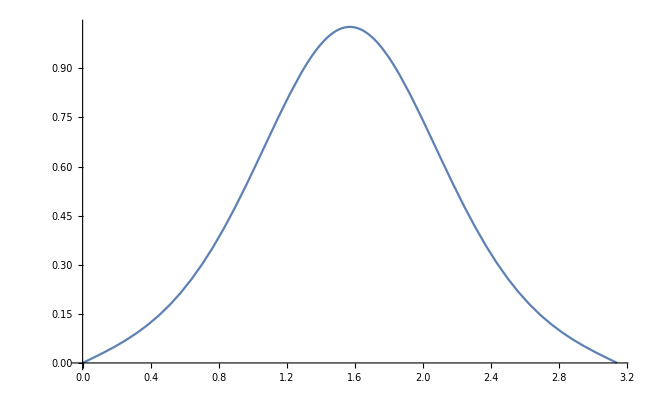

```mathematica
v=0.5;
Plot[(Sin[x](v^2+v^2 Sin[x]^2))/((1-v^2 Sin[x]^2)^(5/2)),{x,0,π}]
```

```mathematica
f1[v_,r_,mD_]:=NIntegrate[(Sin[θ](2+v^2 Sin[θ]^2))/((1-v^2 Sin[θ]^2)^(5/2))(p Exp[ⅈ p r Cos[θ]])/((p^2+Πpar[θ,v,mD])(p^2+Conjugate[Πpar[θ,v,mD]])),{θ,0,π},{p,0,∞}]
```

```mathematica
f[v_,r_,mD_]:=NIntegrate[(Sin[θ](2+v^2 Sin[θ]^2))/((1-v^2 Sin[θ]^2)^(5/2))(p Cos[p r Cos[θ]])/((p^2+Πpar[θ,v,mD])(p^2+Conjugate[Πpar[θ,v,mD]])),{θ,0,π},{p,0,∞}]
```

```mathematica
f[0.5,10,0.15]//AbsoluteTiming
```

$Aborted

```mathematica
f1[0.5,10,0.15]
```

78.0167+5.64931×10^-10 ⅈ

```mathematica
f1[0.5,20,0.15]
```

32.5067-8.52027×10^-10 ⅈ

```mathematica
Log[r √Πpar[θ,v1,mD] Cos[θ]]
```

```mathematica
pres[v1_,mD_,r_]:=-2 NIntegrate[(Sin[θ](2+v1^2 Sin[θ]^2))/((1-v1^2 Sin[θ]^2)^(5/2))1/(2 ⅈ Im[Πpar[θ,v1,mD]])((Sinh[r √Πpar[θ,v1,mD] Cos[θ]]SinhIntegral[r √Πpar[θ,v1,mD] Cos[θ]]-Cosh[r √Πpar[θ,v1,mD] Cos[θ]]CoshIntegral[r √Πpar[θ,v1,mD] Cos[θ]])-(Sinh[r √Conjugate[Πpar[θ,v1,mD]] Cos[θ]]SinhIntegral[r √Conjugate[Πpar[θ,v1,mD]] Cos[θ]]-Cosh[r √Conjugate[Πpar[θ,v1,mD]] Cos[θ]]CoshIntegral[r √Conjugate[Πpar[θ,v1,mD]] Cos[θ]])),{θ,0,π/2}];
```

```mathematica
pres[0.5,0.15,10]
```

78.0167+9.65544×10^-15 ⅈ

```mathematica
f[p_]:=Sign[p]*p*Exp[-I*Sign[p]*p*r]/(p*p+Π)/(p*p+Conjugate[Π])
```

```mathematica
Assuming[r∈Reals,Integrate[f[p],{p,-Infinity,+Infinity}]]
```

Piecewise[{{-(√π (MeijerG[{{0},{}},{{0,0},{1/2}},(r^2 Π)/4]-MeijerG[{{0},{}},{{0,0},{1/2}},1/4 r^2 Conjugate[Π]]))/(Π-Conjugate[Π]), (r==0&&Re[Π]≥0&&Re[√Π]>0&&Re[√Conjugate[Π]]>0)||(r==0&&Im[Π]>0)||(r==0&&Im[Π]<0)}, {1/(Π-Conjugate[Π])√π (-ⅈ ⅇ^(r √Π) √π+ⅈ ⅇ^(r √Conjugate[Π]) √π-MeijerG[{{0},{}},{{0,0},{1/2}},(r^2 Π)/4]+MeijerG[{{0},{}},{{0,0},{1/2}},1/4 r^2 Conjugate[Π]]), (r<0&&Re[Π]≥0&&Re[√Π]>0&&Re[√Conjugate[Π]]>0)||(Im[Π]>0&&r<0)||(Im[Π]<0&&r<0)}, {-1/(Π-Conjugate[Π])ⅇ^(-r √Π-r √Conjugate[Π]) √π (ⅈ ⅇ^(r √Π) √π-ⅈ ⅇ^(r √Conjugate[Π]) √π+ⅇ^(r √Π+r √Conjugate[Π]) MeijerG[{{0},{}},{{0,0},{1/2}},(r^2 Π)/4]-ⅇ^(r √Π+r √Conjugate[Π]) MeijerG[{{0},{}},{{0,0},{1/2}},1/4 r^2 Conjugate[Π]]), (Re[Π]≥0&&r>0&&Re[√Π]>0&&Re[√Conjugate[Π]]>0)||(Im[Π]>0&&r>0)||(Im[Π]<0&&r>0)}, {(√π (ⅈ ⅇ^(ⅈ r √-Π) √π r^3 Π^(3/2)+8 MeijerG[{{1},{}},{{1,2},{3/2}},(r^2 Π)/4]))/(2 r^2 Π^2), (r≥0&&Im[Π]==0&&Π<0&&Re[Π]<0)||(r≥0&&Im[Π]==0&&Π<0&&Re[√Π]≤0)||(r≥0&&Im[Π]==0&&Π<0&&Re[√Conjugate[Π]]≤0)}, {(ⅇ^(-ⅈ r √-Π) √π (ⅈ √π r^3 Π^(3/2)+8 ⅇ^(ⅈ r √-Π) MeijerG[{{1},{}},{{1,2},{3/2}},(r^2 Π)/4]))/(2 r^2 Π^2), (Im[Π]==0&&r<0&&Π<0&&Re[Π]<0)||(Im[Π]==0&&r<0&&Π<0&&Re[√Π]≤0)||(Im[Π]==0&&r<0&&Π<0&&Re[√Conjugate[Π]]≤0)}, {Integrate[(ⅇ^(-ⅈ p r Sign[p]) p Sign[p])/((p^2+Π) (p^2+Conjugate[Π])),{p,-∞,∞},Assumptions→(r∈Reals&&Im[Π]==0&&Π≥0&&Re[Π]<0)||(r∈Reals&&Im[Π]==0&&Π≥0&&Re[√Π]≤0)||(r∈Reals&&Im[Π]==0&&Π≥0&&Re[√Conjugate[Π]]≤0)], True}}]

```mathematica
g[p_]:=p*Exp[-I*p*r]/(p*p+Π)/(p*p+Conjugate[Π])
Assuming[r∈Reals,Integrate[g[p],{p,-Infinity,+Infinity}]]
```

ConditionalExpression[(ⅈ (ⅇ^(-√Π Abs[r])-ⅇ^(-Abs[r] √Conjugate[Π])) π Sign[r])/(Π-Conjugate[Π]),Im[Π]≠0||(Re[Π]≥0&&Re[√Π]>0&&Re[√Conjugate[Π]]>0)]

```mathematica
-1/(Π-Conjugate[Π])ⅇ^(-r √Π-r √Conjugate[Π]) √π (ⅈ ⅇ^(r √Π) √π-ⅈ ⅇ^(r √Conjugate[Π]) √π+ⅇ^(r √Π+r √Conjugate[Π]) MeijerG[{{0},{}},{{0,0},{1/2}},(r^2 Π)/4]-ⅇ^(r √Π+r √Conjugate[Π]) MeijerG[{{0},{}},{{0,0},{1/2}},1/4 r^2 Conjugate[Π]])//FullSimplify
```

$Aborted

## Finite velocity potential

```mathematica
αcont={0.5137193759431391,0.0024666827878353577}; 
σcont={0.16955497884544793,0.0008581023195660334};
ccont={-0.15956635071361625,0.0024752900407607015};
```

```mathematica
Πpar[θ_,v_,mD_]:=mD^2/2((2-2 v^2-v^4 Cos[θ]^2 Sin[θ]^2)/((1-v^2 Sin[θ]^2)^2)-((2+v^2 Sin[θ]^2)(1-v^2)v Cos[θ])/(2(1-v^2 Sin[θ]^2)^(5/2))Log[(v Cos[θ]+√(1-v^2 Sin[θ]^2))/(v Cos[θ]-√(1-v^2 Sin[θ]^2))]);
Πper[θ_,β_,v_,mD_]:=mD^2/2((2-2 v^2-v^4 Cos[β]^2 Sin[θ]^2(1-Cos[β]^2 Sin[θ]^2))/((1-v^2+v^2 Cos[β]^2 Sin[θ]^2)^2)-((2+v^2-v^2 Cos[β]^2 Sin[θ]^2)(1-v^2)v Cos[β]Sin[θ])/(2(1-v^2+v^2 Cos[β]^2 Sin[θ]^2)^2)Log[(v Cos[β]Sin[θ]+√(1-v^2+v^2 Cos[β]^2 Sin[θ]^2))/(v Cos[β]Sin[θ]-√(1-v^2+v^2 Cos[β]^2 Sin[θ]^2))]);
```

```mathematica
f[p_,v_,r_]:=Re[NIntegrate[Sin[θ]Πpar[θ,v,1]Exp[ⅈ p r Cos[θ]],{θ,0,π},WorkingPrecision->10]]
```

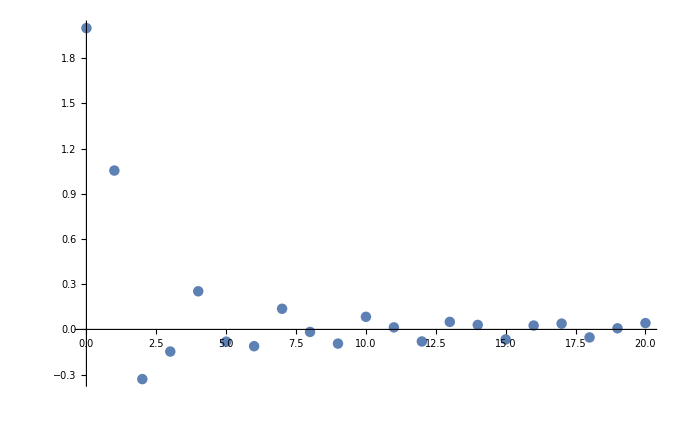

```mathematica
DiscretePlot[f[p,0.1,2],{p,0,20,1},Filling->None,PlotRange->All]
```

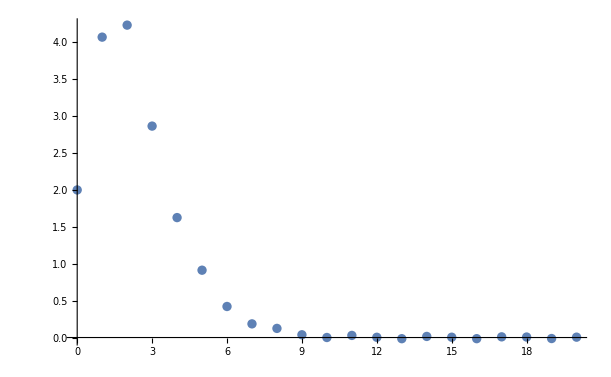

```mathematica
DiscretePlot[f[p,0.9,2],{p,0,20,1},Filling->None,PlotRange->All]
```

```mathematica
ReVcpar[r_,mD_,v_,α_]:=-α/r+α NIntegrate[Sin[θ] √Re[Πpar[θ,v,mD]] Exp[-√Re[Πpar[θ,v,mD]]r Cos[θ]],{θ,0,π/2}];
```

```mathematica
ReVcpar[5,0.15,0.,αcont[[1]]]
```

-0.0485328

```mathematica
-αcont[[1]]/5 Exp[-0.15 5]
```

-0.0485328

```mathematica
ReVcpar[5,0.15,0.,αcont[[1]]]
```

-0.0542111

```mathematica
αcont[[1]]/5+ReVcpar[5,0.15,0.,αcont[[1]]]
```

0.0485328

```mathematica
αcont[[1]]/π NIntegrate[Sin[x](p^2 Exp[ⅈ 5 p Cos[x]])/(p^2+Re[Πpar[x,0.,0.15]]),{p,0,∞},{x,0,π}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {52427.8,0.785398}. NIntegrate obtained 0.296798-2.54782×10^-9 ⅈ and 0.0000993455 for the integral and error estimates.

0.0485329-4.16625×10^-10 ⅈ

```mathematica
αcont[[1]]/π NIntegrate[Sin[x](p^2 Cos[5 p Cos[x]])/(p^2+Re[Πpar[x,0.,0.15]]),{p,0,∞},{x,0,π}]
```

```mathematica
Assuming[θ∈Reals,Integrate[Sin[x](p^2 Exp[ⅈ r p Cos[x]])/(p^2+z[x]),{p,0,∞}]]
```

ConditionalExpression[1/10 ⅈ Sin[x] (2 Sec[x]+5 (2 CosIntegral[-5 ⅈ Cos[x] √z[x]] Sinh[5 Cos[x] √z[x]]+ⅈ Cosh[5 Cos[x] √z[x]] (π+2 ⅈ SinhIntegral[5 Cos[x] √z[x]])) √z[x]),Im[Cos[x]]>0&&(Im[z[x]]≠0||(Re[√z[x]]>0&&Re[z[x]]≥0))]

```mathematica
NIntegrate[Sin[x](p^2 Exp[ⅈ 5 p Cos[x]])/(p^2+Sin[x]),{p,0,∞},{x,0,π}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {52427.8,0.785398}. NIntegrate obtained -0.0280694-2.50066×10^-9 ⅈ and 0.0000970063 for the integral and error estimates.

-0.0280694-2.50066×10^-9 ⅈ

```mathematica
NIntegrate[Sin[x](p^2 Cos[5 p Cos[x]])/(p^2+Sin[x]),{p,0,∞},{x,0,π}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,x} = {37448.1,0.785398}. NIntegrate obtained -0.02807 and 0.0000827911 for the integral and error estimates.

-0.02807

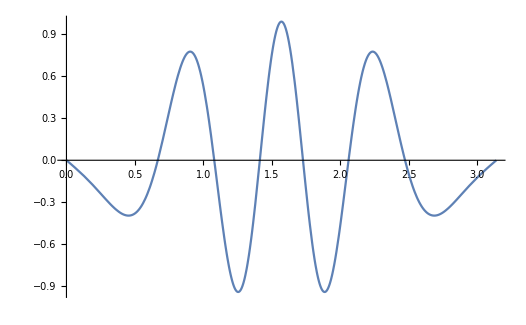

-0.108938

```mathematica
p1=10;
Plot[Sin[x](p1^2 Cos[p1 Cos[x]])/(p1^2+Sin[x]),{x,0,π}]
NIntegrate[Sin[x](p1^2 Cos[p1 Cos[x]])/(p1^2+Sin[x]),{x,0,π}]
```

```mathematica
R=1000;
r=3;
r/π NIntegrate[-ⅈ Sin[y](R^3 Exp[ⅈ 3 x +ⅈ r R Exp[ⅈ x]Cos[y]])/(R^2 Exp[2 ⅈ x]+Sin[y]),{x,0,π},{y,0,π/2}]
```

1.00021+9.9338×10^-16 ⅈ

```mathematica
NIntegrate[Sin[x] √Sin[x] Exp[-√Sin[x]5 Cos[x]],{x,0,π/2}]
```

0.208935

```mathematica
-π NIntegrate[Sin[x] √Sin[x] Exp[-√Sin[x]5 Cos[x]],{x,0,π/2}]+π/5
```

-0.0280711

```mathematica
dat=ParallelTable[{r,αcont[[1]]/π NIntegrate[Sin[x](p^2 Exp[ⅈ r p Cos[x]])/(p^2+Re[Πpar[x,0.5,0.15]]),{p,0,∞},{x,0,π}]},{r,0,10,1}];
```

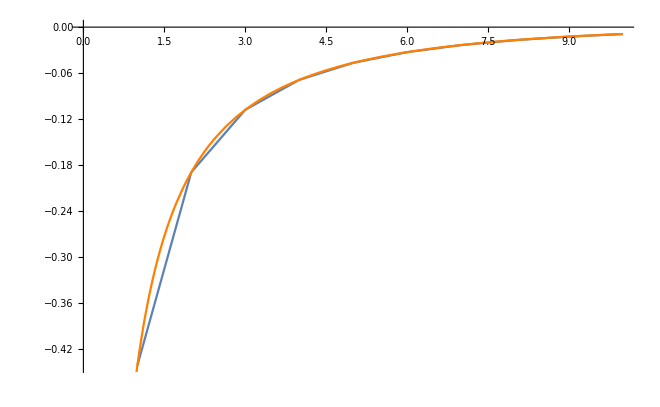

```mathematica
Show[ListPlot[Re[dat[[2;;]]/.{a_,b_}:>{a,-b}],Joined->True],Plot[ReVcpar[r,0.15,0.5,αcont[[1]]],{r,0,10},PlotStyle->Orange]]
```

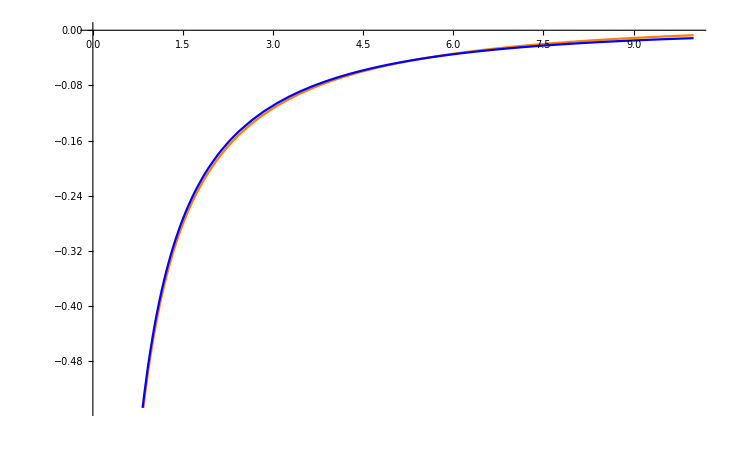

```mathematica
Plot[{ReVcpar[r,0.15,0.8,αcont[[1]]],-αcont[[1]] Exp[-0.15 r]/r},{r,0,10},PlotStyle->{Orange,Blue}]
```

```mathematica
ImVcpar[r_,mD_,v_,α_,T_]:=2(1-v^2)^(3/2)mD^2 α T NIntegrate[(Sin[θ](2+v^2 Sin[θ]^2))/((1-v^2 Sin[θ]^2)^(5/2))1/(2 ⅈ Im[Πpar[θ,v,mD]])((Sinh[r √Πpar[θ,v,mD] Cos[θ]]SinhIntegral[r √Πpar[θ,v,mD] Cos[θ]]-Cosh[r √Πpar[θ,v,mD] Cos[θ]]CoshIntegral[r √Πpar[θ,v,mD] Cos[θ]])-(Sinh[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]]SinhIntegral[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]]-Cosh[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]]CoshIntegral[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]])),{θ,0,π/2}];
```

```mathematica
ImVcpar[5,0.15,0.5,αcont[[1]],0.155]
```

-0.132908+1.73649×10^-17 ⅈ

```mathematica
-(1-0.5^2)^(3/2)0.15^2 αcont[[1]] 0.155 NIntegrate[(Sin[θ](2+0.5^2 Sin[θ]^2))/((1-0.5^2 Sin[θ]^2)^(5/2))(p Exp[ⅈ p 5 Cos[θ]])/((p^2+Πpar[θ,0.5,0.15])(p^2+Conjugate[Πpar[θ,0.5,0.15]])),{θ,0,π},{p,0,∞}]
```

-0.132908-2.59938×10^-15 ⅈ

```mathematica
dat1=ParallelTable[{r,-(1-0.5^2)^(3/2)0.15^2 αcont[[1]] 0.155 NIntegrate[(Sin[θ](2+0.5^2 Sin[θ]^2))/((1-0.5^2 Sin[θ]^2)^(5/2))(p Exp[ⅈ p r Cos[θ]])/((p^2+Πpar[θ,0.5,0.15])(p^2+Conjugate[Πpar[θ,0.5,0.15]])),{θ,0,π},{p,0,∞}]},{r,1,10,1}];
```

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

General::stop: Further output of NIntegrate::mtdfb will be suppressed during this calculation.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

General::stop: Further output of NIntegrate::mtdfb will be suppressed during this calculation.

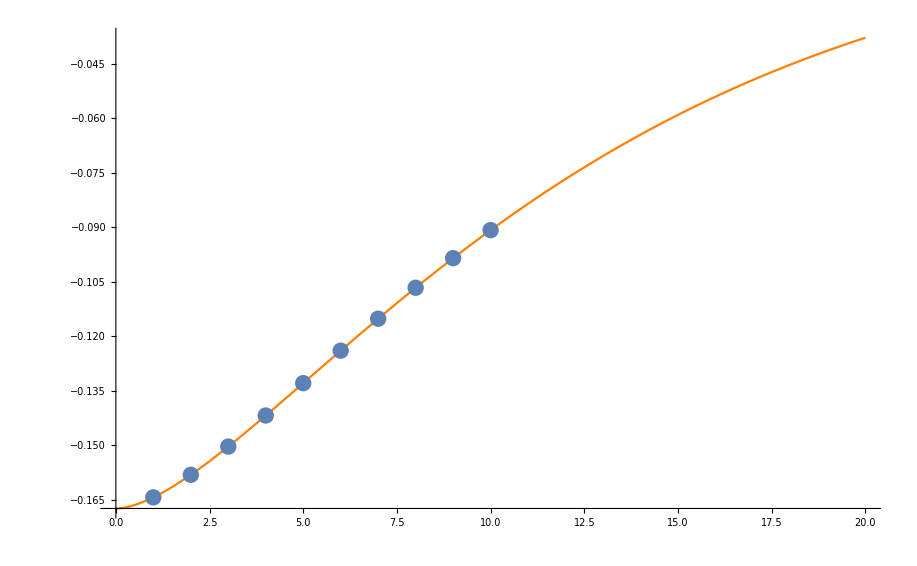

```mathematica
Show[Plot[Re[ImVcpar[r,0.15,0.5,αcont[[1]],0.155]],{r,0,20},PlotStyle->Orange],ListPlot[Re[dat1]]]
```

```mathematica
f[p_,r_]:=Integrate[Sin[x]Re[Πpar[x,0.5,0.15]]Cos[Cos[p r x]],{x,0,π}]
```

```mathematica
f[1,1]
```

$Aborted

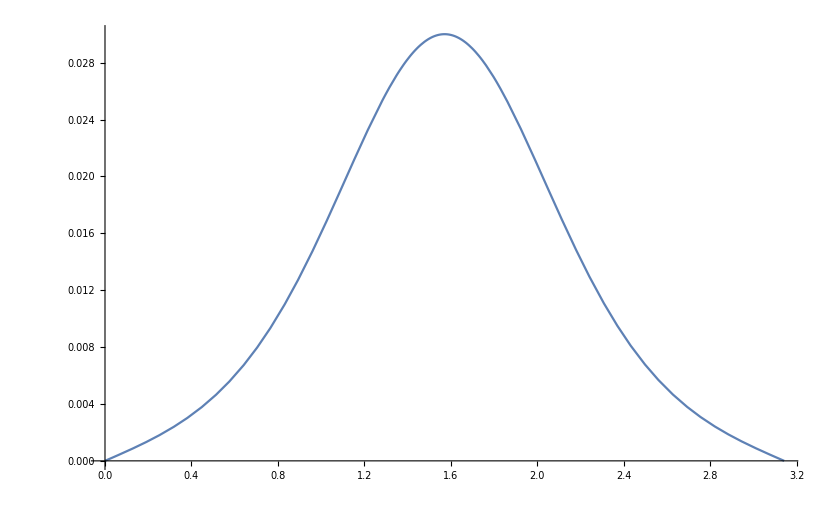

```mathematica
Plot[Sin[x]Re[Πpar[x,0.5,0.15]]Cos[Cos[x]],{x,0,π}]
```

```mathematica
Integrate[(p Exp[- p Cos[θ]])/((-p^2+z)(-p^2+Conjugate[z])),{p,0,∞}]
```

ConditionalExpression[1/(z-Conjugate[z])(-Cos[√-z Cos[θ]] CosIntegral[√-z Cos[θ]]+Cos[√(-Conjugate[z]) Cos[θ]] CosIntegral[√(-Conjugate[z]) Cos[θ]]+1/2 Sin[√-z Cos[θ]] (π-2 SinIntegral[√-z Cos[θ]])-1/2 Sin[√(-Conjugate[z]) Cos[θ]] (π-2 SinIntegral[√(-Conjugate[z]) Cos[θ]])),Re[Cos[θ]]>0&&((Im[√z]≠0&&Im[z]≠0&&Im[√Conjugate[z]]≠0)||Re[z]<0)]

```mathematica
Integrate[(p Exp[- ⅈ p Cos[θ]])/((-p^2+z)(-p^2+Conjugate[z])),{p,0,∞}]
```

ConditionalExpression[1/(z-Conjugate[z])(-Cosh[√(-1/z) z Cos[θ]] CosIntegral[(ⅈ Cos[θ])/(√(-1/z))]+Cosh[√(-1/Conjugate[z]) Conjugate[z] Cos[θ]] CosIntegral[(ⅈ Cos[θ])/(√(-1/Conjugate[z]))]+1/2 Sinh[√(-1/z) z Cos[θ]] (-ⅈ π+2 SinhIntegral[√(-1/z) z Cos[θ]])+1/2 ⅈ Sinh[√(-1/Conjugate[z]) Conjugate[z] Cos[θ]] (π+2 ⅈ SinhIntegral[√(-1/Conjugate[z]) Conjugate[z] Cos[θ]])),Im[Cos[θ]]<0&&Im[√Conjugate[z]]≠0&&Im[√z]≠0]

```mathematica
Assuming[θ∈Reals,Integrate[(p Exp[ⅈ p r Cos[θ]])/((p^2+z)(p^2+Conjugate[z])),{p,0,∞}]]//FullSimplify
```

ConditionalExpression[-1/(4 Im[z])ⅈ (2 Cosh[r √z Cos[θ]] CosIntegral[-ⅈ r √z Cos[θ]]-2 Cosh[r √Conjugate[z] Cos[θ]] CosIntegral[-ⅈ r √Conjugate[z] Cos[θ]]+ⅈ π (Sinh[r √z Cos[θ]]-Sinh[r √Conjugate[z] Cos[θ]])-2 Sinh[r √z Cos[θ]] SinhIntegral[r √z Cos[θ]]+2 Sinh[r √Conjugate[z] Cos[θ]] SinhIntegral[r √Conjugate[z] Cos[θ]]),((Cos[θ]<0&&Im[r]<0)||(Cos[θ]>0&&Im[r]>0))&&((z≠Re[z]&&Re[√z]≠0&&Re[√Conjugate[z]]≠0)||(Re[√z]>0&&Re[√Conjugate[z]]>0&&Re[z]≥0))]

```mathematica
Assuming[θ∈Reals,Integrate[(p^3 Exp[ⅈ p r Cos[θ]])/((p^2+z)(p^2+Conjugate[z])),{p,0,∞}]]//FullSimplify
```

ConditionalExpression[(ⅈ (z MeijerG[{{-1},{}},{{-1,0,1/2},{}},-1/4 r^2 z Cos[θ]^2]-Conjugate[z] MeijerG[{{-1},{}},{{-1,0,1/2},{}},-1/4 r^2 Conjugate[z] Cos[θ]^2]))/(4 √π Im[z]),((Cos[θ]<0&&Im[r]<0)||(Cos[θ]>0&&Im[r]>0))&&((z≠Re[z]&&Re[√z]≠0&&Re[√Conjugate[z]]≠0)||(Re[√z]>0&&Re[√Conjugate[z]]>0&&Re[z]≥0))]

```mathematica
Assuming[θ∈Reals,Integrate[(p^2 Exp[ⅈ p r Cos[θ]])/((p^2+z)(p^2+Conjugate[z])),{p,0,∞}]]//FullSimplify
```

ConditionalExpression[1/(4 Im[z])(√z (-2 CosIntegral[-ⅈ r √z Cos[θ]] Sinh[r √z Cos[θ]]+Cosh[r √z Cos[θ]] (-ⅈ π+2 SinhIntegral[r √z Cos[θ]]))+√Conjugate[z] (2 CosIntegral[-ⅈ r √Conjugate[z] Cos[θ]] Sinh[r √Conjugate[z] Cos[θ]]+ⅈ Cosh[r √Conjugate[z] Cos[θ]] (π+2 ⅈ SinhIntegral[r √Conjugate[z] Cos[θ]]))),((Cos[θ]<0&&Im[r]<0)||(Cos[θ]>0&&Im[r]>0))&&((z≠Re[z]&&Re[√z]≠0&&Re[√Conjugate[z]]≠0)||(Re[√z]>0&&Re[√Conjugate[z]]>0&&Re[z]≥0))]

```mathematica
Assuming[θ∈Reals,Integrate[(p^2 Exp[ⅈ p r Cos[θ]])/(p^2+z),{p,0,∞}]]//FullSimplify
```

ConditionalExpression[(ⅈ √z (ⅈ π r Cosh[r √z Cos[θ]]+(2 Sec[θ])/(√z)+2 r CosIntegral[-ⅈ r √z Cos[θ]] Sinh[r √z Cos[θ]]-2 r Cosh[r √z Cos[θ]] SinhIntegral[r √z Cos[θ]]))/(2 r),((Cos[θ]<0&&Im[r]<0)||(Cos[θ]>0&&Im[r]>0))&&((Im[z]≠0&&Re[√z]≠0)||(Re[√z]>0&&Re[z]≥0))]